### Plot Options ( Fixed some rules for ListPlot and so on... )

```mathematica
myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.005;
size=0.05;
font="Latin Modern Roman";
imagSize=240;
fontSize=10;

SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];


fTXT[txt_]:=Text[Style[txt,FontFamily->font,FontSize->fontSize]]
itTXT[txt_]:=Text[Style[txt,FontFamily->font,FontSize->fontSize,FontColor->Black,FontSlant->Italic]]
sTXT[txt_,size_]:=Text[Style[txt,FontFamily->font,FontSize->size]]

getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]
```

### Diagonalization -- this time with the right periodicity of the BZ :)

```mathematica
Clear[H,xx,yy,ll,rr]
```

```mathematica
(*forget about ϕ at the moment, it will be just a shift in the momentum ... *)
H[k_]=(1-Cos[k])PauliMatrix[1]+Sin[k]PauliMatrix[3];
$Assumptions=Element[{ϕ,k,kp,q},Reals];
MatrixForm[H[k]]
```

```mathematica
(*solution made explicitly periodic outside the interval (-π,π)*)
(*Mod[k,2π,-π]==(Mod[k+π,2π]-π)*)
xx[k_]=Cos[Mod[k,2π,-π]/4];
yy[k_]=Sin[Mod[k,2π,-π]/4];
rr[k_]={xx[k],yy[k]};
ll[k_]={-yy[k],xx[k]};
ee[k_]=2 Sin[Mod[k,2π,-π]/2];

U[k_]=FullSimplify[{rr[k],ll[k]}*];
MatrixForm[U[k]]

kmax=6;
FullSimplify[rr[k].rr[k]==ll[k].ll[k]==1]
FullSimplify[U[k].H[k].U[k]†==ee[k] PauliMatrix[3]]
(*Chop[
NMaxValue[{#,-kmax≤k≤kmax},k]&/@Flatten[Abs[%]]
]=={0,0,0,0}*)
```

#### plotting the dispersion & the components of the solution

```mathematica
kmax=5;
Plot[Evaluate[ee[k π]{+1,-1}],{k,-kmax,kmax},
PlotRange->{-2,2},
PlotStyle->{{Thick,Orange},{Thick,Green}},
PlotLegends->Placed[LineLegend[{Orange,Green},{"r","l"}],{Right,Center}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","ω"},GridLines->None
]

Show[
Plot[ee[k π],{k,-kmax,kmax},
ColorFunction->Function[{x,y},ColorData["LightTemperatureMap"][(rr[(x-0.5)*2 kmax π][[1]])^2]],
PlotStyle->Thick,
PlotRange->{-2,2}
],
Plot[-ee[k π],{k,-kmax ,kmax },
ColorFunction->Function[{x,y},ColorData["LightTemperatureMap"][(ll[(x-0.5)*2 kmax π][[1]])^2]],
PlotStyle->Thick,
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Right,Center}]
],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","ω"},GridLines->None]
Plot[Evaluate[rr[k π]],{k,-kmax,kmax},
PlotRange->{-1.1,1.1},
PlotStyle->{{Thick,ColorData["LightTemperatureMap"][1]},{Thick,ColorData["LightTemperatureMap"][0]}},
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Right,Bottom}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","r comp."},GridLines->None
]
Plot[Evaluate[ll[k π]],{k,-kmax,kmax},
PlotRange->{-1.1,1.1},
PlotStyle->{{Thick,ColorData["LightTemperatureMap"][1]},{Thick,ColorData["LightTemperatureMap"][0]}},
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Left,Bottom}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","l comp."},GridLines->None
]
```

### Amplitudes of interaction processes

```mathematica
(*m denotes the flavour r/l of the eigenmode;
s,sp the spin character u/d of the physical particles subject to interaction*)
ff[s_,sp_][k_,kp_,q_][m1_,m2_,m3_,m4_]:=U[k+q][[m1,s]]*U[kp-q][[m2,sp]]*U[kp][[m3,sp]]U[k][[m4,s]]//FullSimplify
```

#### combinatorics of the different processes

```mathematica
tab11=Array[
ff[1,1][k,kp,q]
,{2,2,2,2}]//FullSimplify

tab22=Array[
ff[2,2][k,kp,q]
,{2,2,2,2}]//FullSimplify;

tab12=Array[
ff[1,2][k,kp,q]
,{2,2,2,2}]//FullSimplify;

tab21=Array[
ff[2,1][k,kp,q]
,{2,2,2,2}]//FullSimplify;
```

```mathematica
(*ONLY the 16 elements of (1,1) are relevant, all others can be obtained by permutations and minus prefactors!!*)
```

```mathematica
Map[Position[tab11,#]&,tab11,{4}]
Length[Flatten[%,4]]

Map[Position[tab11,#]&,-tab11,{4}]
Length[Flatten[%,4]]
```

```mathematica
Map[Position[tab11,#]&,tab22,{4}]
Length[Flatten[%,4]]
Map[Position[tab11,#]&,-tab22,{4}]
Length[Flatten[%,4]]
```

```mathematica
Map[Position[tab11,#]&,tab12,{4}]
Length[Flatten[%,4]]
Map[Position[tab11,#]&,-tab12,{4}]
Length[Flatten[%,4]]
```

```mathematica
Map[Position[tab11,#]&,tab21,{4}]
Length[Flatten[%,4]]
Map[Position[tab11,#]&,-tab21,{4}]
Length[Flatten[%,4]]
```

```mathematica
Map[Position[tab12,#]&,tab21,{4}]==Map[Position[tab11,#]&,tab22,{4}]
Map[Position[tab12,#]&,-tab21,{4}]==Map[Position[tab11,#]&,-tab22,{4}]
```

#### plotting the amplitudes of the different processes -- here only for UP-UP

```mathematica
terms=Flatten[Array[{#1,#2,#3,#4}&,{2,2,2,2}],3];

mlab={"r","l"};
label[m1_,m2_,m3_,m4_]:=""<>mlab[[m1]]<>"†(k_1+q)"<>mlab[[m2]]<>"†(k_2-q)"<>mlab[[m3]]<>"(k_2)"<>mlab[[m4]]<>"(k_1)"

Manipulate[
{m1,m2,m3,m4}=bsintra;
{n1,n2,n3,n4}=bsinter;
TableForm[
{
"k_2/2="<>ToString[Chop[(k2-k1)/2//N]]<>";    -k_2/2="<>ToString[Chop[-(k1+k2)/2//N]],
Plot[
Evaluate[
{
ff[1,1][k1*π,k2*π,q*π][m1,m2,m3,m4]Cos[q*π],
ff[2,2][k1*π,k2*π,q*π][m1,m2,m3,m4]Cos[q*π],
(ff[1,1][k1*π,k2*π,q*π][m1,m2,m3,m4]+
ff[2,2][k1*π,k2*π,q*π][m1,m2,m3,m4])Cos[q*π]
}],{q,-2,2},
PlotLabel->
label[m1,m2,m3,m4],
PlotStyle->{myred,myblue,{Dashed,Black},Black},FrameLabel->{"q/π","Amplitude of process"},
(*GridLines->{{1+(k2-k1)/2},{}},*)
PlotRange->{-1,1},
PlotLegends->Placed[{"n_(↑j)n_(↑j + 1)","n_(↓j)n_(↓j + 1)", "sum"},{Left,Bottom}]
],
Plot[
Evaluate[
{ff[1,2][k1*π,k2*π,q*π][n1,n2,n3,n4]Cos[q*π],
ff[2,1][k1*π,k2*π,q*π][n1,n2,n3,n4]Cos[q*π],
(ff[1,2][k1*π,k2*π,q*π][n1,n2,n3,n4]+
ff[2,1][k1*π,k2*π,q*π][n1,n2,n3,n4])Cos[q*π]
}],{q,-2,2},
PlotLabel->
label[n1,n2,n3,n4],
PlotStyle->{mygreen,myyellow,{Dashed,Black},Black},FrameLabel->{"q/π","Amplitude of process"},
(*GridLines->{{2+(k2-k1)/2,-2+(k2-k1)/2},{}},*)
PlotRange->{-1,1},
PlotLegends->Placed[{"n_(↑j)n_(↓j + 1)","n_(↓j)n_(↑j + 1)", "sum"},{Left,Bottom}]
],
Plot[
Evaluate[
{ff[1,2][k1*π,k2*π,q*π][n1,n2,n3,n4],
ff[2,1][k1*π,k2*π,q*π][n1,n2,n3,n4],
(ff[1,2][k1*π,k2*π,q*π][n1,n2,n3,n4]+
ff[2,1][k1*π,k2*π,q*π][n1,n2,n3,n4])
}],{q,-2,2},
PlotLabel->
label[n1,n2,n3,n4],
PlotStyle->{mygreen,myyellow,{Dashed,Black},Black},FrameLabel->{"q/π","Amplitude of process"},
(*GridLines->{{2+(k2-k1)/2,-2+(k2-k1)/2},{}},*)
PlotRange->{-1,1},
PlotLegends->Placed[{"n_(↑j)n_(↓j)","n_(↓j)n_(↑j)", "sum"},{Left,Bottom}]
]
(*{intra:(fintra= FullSimplify[ff[Subscript[k, 1],Subscript[k, 2],q,bsintra,1,1]+ff[Subscript[k, 1],Subscript[k, 2],q,bsintra,2,2]])},*)
(*inter:(finter=FullSimplify[formfactor[Subscript[k, 1],Subscript[k, 2],q,bsinter,1,2]+formfactor[Subscript[k, 1],Subscript[k, 2],q,bsinter,2,1]]),*)
}
]
,{{k1,0.0},-1.,1.},{{k2,0.0},-1.,1.}, {bsintra,terms}, {bsinter,terms}
]
```

### Diagonalization -- do not care of the periodicity in k, we will inverse Fourier transform

```mathematica
Clear[H,xx,yy,ll,rr]
```

```mathematica
(*forget about ϕ at the moment, it will be just a shift in the momentum ... *)
H[k_]=(1-Cos[k])PauliMatrix[1]+Sin[k]PauliMatrix[3];
$Assumptions=Element[{ϕ,k,kp,q},Reals];
MatrixForm[H[k]]
```

(Sin[k] | 1-Cos[k]
1-Cos[k] | -Sin[k])

```mathematica
(*solution made explicitly periodic outside the interval (-π,π)*)
(*Mod[k,2π,-π]==(Mod[k+π,2π]-π)*)
xx[k_]=Cos[k/4];
yy[k_]=Sin[k/4];
rr[k_]={xx[k],yy[k]};
ll[k_]={-yy[k],xx[k]};
ee[k_]=2 Sin[k/2];

U[k_]=FullSimplify[{rr[k],ll[k]}*];
MatrixForm[U[k]]

kmax=6;
FullSimplify[rr[k].rr[k]==ll[k].ll[k]==1]
FullSimplify[U[k].H[k].U[k]†==ee[k] PauliMatrix[3]]
(*Chop[
NMaxValue[{#,-kmax≤k≤kmax},k]&/@Flatten[Abs[%]]
]=={0,0,0,0}*)
```

(Cos[k/4] | Sin[k/4]
-Sin[k/4] | Cos[k/4])

True

True

#### plotting the dispersion & the components of the solution

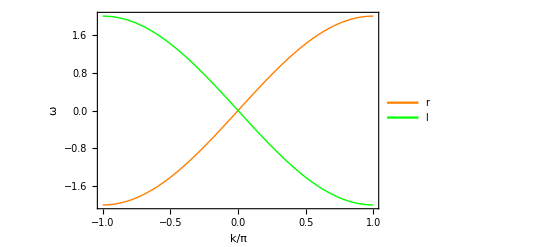

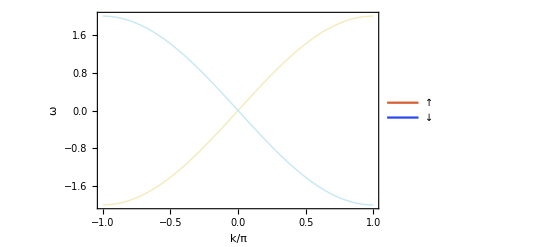

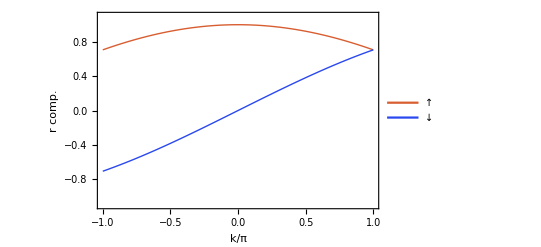

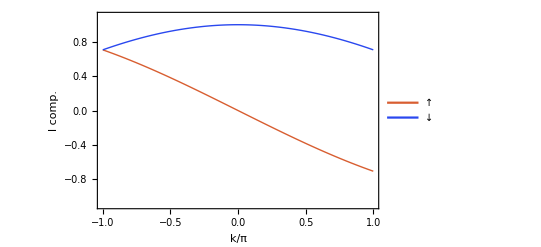

```mathematica
kmax=1;
Plot[Evaluate[ee[k π]{+1,-1}],{k,-kmax,kmax},
PlotRange->{-2,2},
PlotStyle->{{Thick,Orange},{Thick,Green}},
PlotLegends->Placed[LineLegend[{Orange,Green},{"r","l"}],{Right,Center}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","ω"},GridLines->None
]

Show[
Plot[ee[k π],{k,-kmax,kmax},
ColorFunction->Function[{x,y},ColorData["LightTemperatureMap"][(rr[(x-0.5)*2 kmax π][[1]])^2]],
PlotStyle->Thick,
PlotRange->{-2,2}
],
Plot[-ee[k π],{k,-kmax ,kmax },
ColorFunction->Function[{x,y},ColorData["LightTemperatureMap"][(ll[(x-0.5)*2 kmax π][[1]])^2]],
PlotStyle->Thick,
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Right,Center}]
],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","ω"},GridLines->None]
Plot[Evaluate[rr[k π]],{k,-kmax,kmax},
PlotRange->{-1.1,1.1},
PlotStyle->{{Thick,ColorData["LightTemperatureMap"][1]},{Thick,ColorData["LightTemperatureMap"][0]}},
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Right,Bottom}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","r comp."},GridLines->None
]
Plot[Evaluate[ll[k π]],{k,-kmax,kmax},
PlotRange->{-1.1,1.1},
PlotStyle->{{Thick,ColorData["LightTemperatureMap"][1]},{Thick,ColorData["LightTemperatureMap"][0]}},
PlotLegends->Placed[LineLegend[{ColorData["LightTemperatureMap"][1],ColorData["LightTemperatureMap"][0]},{"↑","↓"}],{Left,Bottom}],
AspectRatio->1/GoldenRatio,ImageSize->400,
FrameLabel->{"k/π","l comp."},GridLines->None
]
```

#### spin-to-direction transform in real-space coordinates

```mathematica
Clear[T,To]
T[L_,y_]=(4 ⅈ)/L FullSimplify[∑_(nk=1)^(L/2-1) Sin[π/L nk]Sin[(2π)/L nk y],y ∈ Integers]
```

-(2 ⅈ (-1)^y Sin[(2 π y)/L])/(L (Cos[π/L]-Cos[(2 π y)/L]))

```mathematica
test[L_,y_]=FullSimplify[(2ⅈ)/L*∑_(nk=1)^(L/2-1) Sin[π/(2L)nk]Sin[(2π)/L nk y],y ∈ Integers&&L∈Integers]
```

(ⅈ (-1)^y (-Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]+Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]))/(2 L)

```mathematica
test2[L_,y_]=(ⅈ (-1)^y (Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]-Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]))/(2 L)
```

(ⅈ (-1)^y (Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]-Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]))/(2 L)

```mathematica
test[L,x]
```

(ⅈ (-1)^x (-Cos[(π (1+L+4 x))/(4 L)] Csc[(π+4 π x)/(4 L)]+Csc[(π-4 π x)/(4 L)] Sin[(π (-1+L+4 x))/(4 L)]))/(2 L)

```mathematica
FullSimplify[Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]+Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]
,y∈Integers&&L>0]
```

Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]+Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]

```mathematica
Chop[Table[test[20,y],{y,0,5}]//N]
Chop[Table[test2[20,y],{y,0,5}]//N]
```

{0,0.+0.23823 ⅈ,0.-0.110598 ⅈ,0.+0.0699116 ⅈ,0.-0.0488805 ⅈ,0.+0.0354647 ⅈ}

{0,0.-0.23823 ⅈ,0.+0.110598 ⅈ,0.-0.0699116 ⅈ,0.+0.0488805 ⅈ,0.-0.0354647 ⅈ}

```mathematica
Clear[TTL]
TTL[y_]=Limit[T[L,y],L->∞]
```

(8 ⅈ ⅇ^(ⅈ π y) y)/(π-4 π y^2)

```mathematica
T[10,0]
```

0

```mathematica
Clear[ϕ,R,Rc,Rs,L,y]
(*little trick to avoid ambiguities at finite L values:
we sum over all momenta different from ±π, and then take 1/2 of each π value*)
(*R[L_,y_]=FullSimplify[1/L(∑_(nk=-L/2+1)^(L/2-1) U[(2π)/L nk] ⅇ^(ⅈ (2π)/L nk y)+1/2(U[-π] ⅇ^(-ⅈ π y)+U[π] ⅇ^(+ⅈ π y))),y ∈ Integers]*)

(*otherwise said, we exploit the parity (even/odd) of the U matrix elements and simplify the sums quite a bit, avoiding false friends...*)
Rc[L_,y_]=FullSimplify[1/L(1+(-1)^y(√2)/2+2∑_(nk=1)^(L/2-1) Cos[π/(2L)nk]Cos[(2π)/L nk y]),y ∈ Integers]
Rs[L_,y_]=FullSimplify[1/L(2ⅈ∑_(nk=1)^(L/2-1) Sin[π/(2L)nk]Sin[(2π)/L nk y]),y ∈ Integers]


(*there are even good defined and nice-looking limits for the thermodynamic limit!*)
RcTL[y_]=Limit[Rc[L,y],L->+∞]
RsTL[y_]=Limit[Rs[L,y],L->+∞]

(*and noticeably just a factor between the two, which explains the difference in decay later on ;) *)
FullSimplify[RsTL[y]/RcTL[y]]
```

((-1)^y (√2+Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]+Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]))/(2 L)

(ⅈ (-1)^y (-Cos[(π (1+L+4 y))/(4 L)] Csc[(π+4 π y)/(4 L)]+Csc[(π-4 π y)/(4 L)] Sin[(π (-1+L+4 y))/(4 L)]))/(2 L)

(2 √2 ⅇ^(ⅈ π y))/(π-16 π y^2)

(8 ⅈ √2 ⅇ^(ⅈ π y) y)/(π-16 π y^2)

4 ⅈ y

```mathematica
FullSimplify[Table[-((8+8 ⅈ) (-1)^(1/4+y) y)/(π (-1+16 y^2)),{y,0,5}]]//N
```

{0.,0.+0.240084 ⅈ,0.-0.114326 ⅈ,0.+0.075551 ⅈ,0.-0.0564904 ⅈ,0.+0.0451286 ⅈ}

```mathematica
Table[RsTL[y],{y,0,5}]//N//Chop
```

{0,0.+0.240084 ⅈ,0.-0.114326 ⅈ,0.+0.075551 ⅈ,0.-0.0564904 ⅈ,0.+0.0451286 ⅈ}

```mathematica
-RcTL[0]^2RsTL[1]^2//N
```

0.0467216

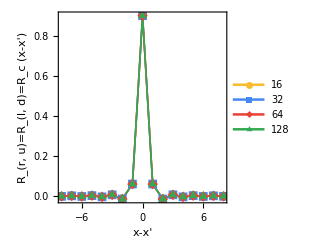

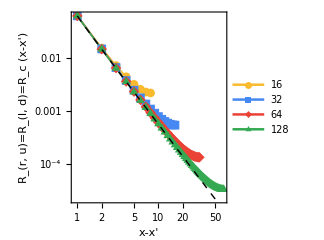

```mathematica
Clear[L]
Ltable={16,32,64,128};
Show[
ListPlot[
Table[Table[{y,Rc[L,y]},{y,-8,8}],{L,Ltable}],
PlotMarkers->Automatic,PlotRange->All,
FrameLabel->{"x-x'","R_(r, u)=R_(l, d)=R_c (x-x')"},
PlotLegends->Placed[Ltable,{Right,Top}],
GridLines->None
]
]
Show[
ListLogLogPlot[
Table[Table[{y,Abs[Re[Rc[L,y]]]},{y,1,L/2}],{L,Ltable}],
PlotMarkers->Automatic,PlotRange->All,Frame->True,
FrameLabel->{"x-x'","R_(r, u)=R_(l, d)=R_c (x-x')"},
PlotLegends->Placed[Ltable,{Right,Top}],
GridLines->None
]
,
LogLogPlot[
Abs[RcTL[y]],{y,1,Max[Ltable]/2},
PlotStyle->{Thick,Dashed,Black}
]
]
```

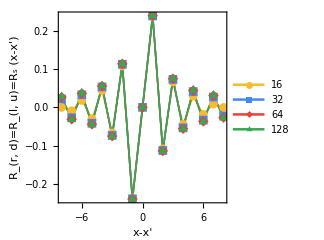

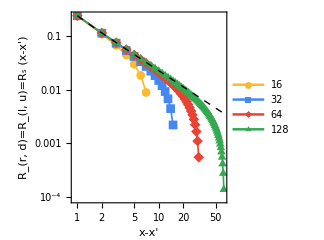

```mathematica
Clear[L]
Ltable={16,32,64,128};
ListPlot[
Table[Table[{y,Im[Rs[L,y]]},{y,-8,8}],{L,Ltable}],
PlotMarkers->Automatic,PlotRange->All,
FrameLabel->{"x-x'","R_(r, d)=R_(l, u)=R_s (x-x')"},
PlotLegends->Placed[Ltable,{Left,Top}],
GridLines->None
]
Show[
ListLogLogPlot[
Table[Table[{y,Abs[Im[Rs[L,y]]]},{y,1,L/2}],{L,Ltable}],
PlotMarkers->Automatic,PlotRange->All,Frame->True,
FrameLabel->{"x-x'","R_(r, d)=R_(l, u)=R_s (x-x')"},
PlotLegends->Placed[Ltable,{Left,Bottom}],
GridLines->None
]
,
LogLogPlot[
Abs[RsTL[y]],{y,1,Max[Ltable]/2},
PlotStyle->{Thick,Dashed,Black}
]
]
```

```mathematica
RcTL[1]//N
```

0.0600211

```mathematica
FullSimplify[RcTL[x+1]+RcTL[x],x∈Reals]
```

-(32 √2 ⅇ^(ⅈ π x) (1+2 x))/(π (3+4 x) (5+4 x) (-1+16 x^2))

```mathematica
Im[Conjugate[RsTL[1]]]
Im[Conjugate[RsTL[-1]]]
```

-(8 √2)/(15 π)

(8 √2)/(15 π)

```mathematica
RcTL[x]*(-1-4/(3+4 x)+12/(5+4 x))/.{x->1}
```

-(2 √2)/(63 π)

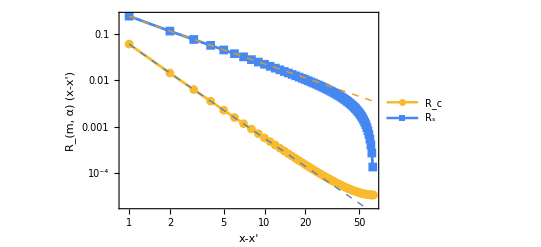

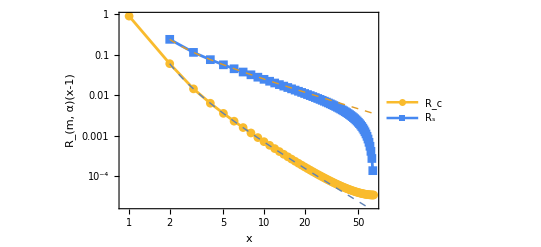

```mathematica
(*the behaviour is overall very similar to the one of the flat-band case (see the notes),
modulo tiny details, like the amount of neighbours to be involved in the next round of approximation...*)

L0=128;
Show[
ListLogLogPlot[
{Table[{y,Abs[Re[Rc[L0,y]]]},{y,1,L0/2}],Table[{y,Abs[Im[Rs[L0,y]]]},{y,1,L0/2}]},
PlotMarkers->Automatic,PlotRange->All,Frame->True,
FrameLabel->{"x-x'","R_(m, α) (x-x')"},
PlotLegends->Placed[{"R_c","R_s"},{Right,Top}],
AspectRatio->1/GoldenRatio,ImageSize->400
]
,
LogLogPlot[
{Abs[RcTL[y]],Abs[RsTL[y]]},{y,1,Max[Ltable]/2},
PlotStyle->{{Thick,Dashed}}
]
]

Show[
ListLogLogPlot[
{Table[{y+1,Abs[Re[Rc[L0,y]]]},{y,0,L0/2}],Table[{y+1,Abs[Im[Rs[L0,y]]]},{y,0,L0/2}]},
PlotMarkers->Automatic,PlotRange->All,Frame->True,
FrameLabel->{"x","R_(m, α)(x-1)"},
PlotLegends->Placed[{"R_c","R_s"},{Right,Top}],
AspectRatio->1/GoldenRatio,ImageSize->400
],
LogLogPlot[
{Abs[RcTL[y-1]],Abs[RsTL[y-1]]},{y,2,Max[Ltable]/2},
PlotStyle->{{Thick,Dashed}}
]
]
```

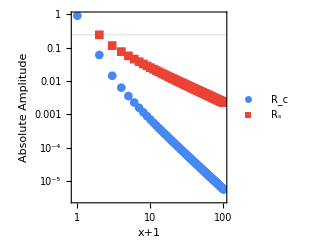

```mathematica
ListLogLogPlot[
{
Table[RcTL[y]//Abs,{y,0,100}],
Table[RsTL[y]//Abs,{y,0,100}]
}
,PlotStyle->{myblue,myred,mygreen}
,Joined->False,GridLines->{{},{RsTL[1.0]//Abs}}
,PlotRange->Full
,PlotMarkers->Automatic
,PlotLegends->Placed[{"R_c","R_s","T"},{Left,Bottom}]
,FrameLabel->{"x+1","Absolute Amplitude"}]
```

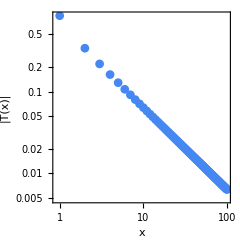

```mathematica
ListLogLogPlot[
{
Table[TTL[y]//Abs,{y,1,100}]
}
,PlotStyle->{myblue,myred,mygreen}
,Joined->False,GridLines->None
,PlotRange->Full
,PlotMarkers->Automatic
,FrameLabel->{"x","|T(x)|"}]
```

### Bosonization

#### Definition of non-commutative expressions & simplification of exponents

```mathematica
(*Import["http://www.feyncalc.org/install.m"]*)
```

```mathematica
Quiet@Needs@"HighEnergyPhysics`FeynCalc`";
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
(*FI;*)
```

Loading FeynCalc from /Users/mrizzi/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

```mathematica
(*declare which variables are non-commutative, 
and define the Baker-Campbell-Hausdorff formula (here exact, since commutator will be a number)*)
DeclareNonCommutative[ϕ,ϕpr,θ,θpr];

(* Matteo inserted this notation, to avoid any bookkeeping issues with primes and so on ;-) *)
Commutator[ϕ[x1_],θ[x2_]]=ⅈ*π*HeavisideTheta[x2-x1]
Commutator[ϕ[x1_],ϕ[x2_]]=0
Commutator[θ[x1_],θ[x2_]]=0

Clear[bchFormula,A,B]
bchFormula[A_,B_]:=DotSimplify@(A+B+1/2 Commutator[A,B])
bchFormula2[A_,B_]:=Coefficient[A,ⅇ,Exponent[A,ⅇ]]Coefficient[B,ⅇ,Exponent[B,ⅇ]] ⅇ^bchFormula[Exponent[A,ⅇ],Exponent[B,ⅇ]]

(*DotSimplify@ⅇ^(Exponent[A,ⅇ]+Exponent[B,ⅇ]+1/2 Commutator[Exponent[A,ⅇ],Exponent[B,ⅇ]])*)


(*define the point-splitting procedure in a compact way -- 
for now with A & B monomers, not yet polynomials, sorry*)
psprod[A_,B_][ϵ_]:=Refine[1/2(bchFormula2[A/.{x->x+ϵ},B]+bchFormula2[A/.{x->x-ϵ},B]),ϵ>0]

psprode[A_,B_][ϵ_]:=Series[psprod[A,B][ϵ],{ϵ,0,3}]
psproda[A_,B_]:=Refine[psprode[A,B][a],a>0]
psprodlim[A_,B_]:=Refine[Limit[psproda[A,B],a->0,Direction->"FromAbove"]]

(*to be used when both are polynomials... notice that it might be different to perform the sum of the limits or the limit of the sum...*)
psprodsum[A_,B_][ϵ_]:=∑_(ii=1)^Length[A] ∑_(jj=1)^Length[B] psprod[A[[ii]],B[[jj]]][ϵ]
psprodesum[A_,B_][ϵ_]:=∑_(ii=1)^Length[A] ∑_(jj=1)^Length[B] psprode[A[[ii]],B[[jj]]][ϵ]
psprodasum[A_,B_]:=∑_(ii=1)^Length[A] ∑_(jj=1)^Length[B] psproda[A[[ii]],B[[jj]]]
psprodlimsum[A_,B_]:=Refine[Limit[Series[Normal[psprodasum[A,B]],{a,0,3}],a->0,Direction->"FromAbove"]]


(*to be used when the first is a polynomial*)
psprodsum1[A_,B_][ϵ_]:=∑_(ii=1)^Length[A] psprod[A[[ii]],B][ϵ]
psprodesum1[A_,B_][ϵ_]:=∑_(ii=1)^Length[A] psprode[A[[ii]],B][ϵ]
psprodasum1[A_,B_]:=∑_(ii=1)^Length[A] psproda[A[[ii]],B]
psprodlimsum1[A_,B_]:=Refine[Limit[Series[Normal[psprodasum1[A,B]],{a,0,3}],a->0,Direction->"FromAbove"]]


(*to be used when the second is a polynomial*)
psprodsum2[A_,B_][ϵ_]:=∑_(jj=1)^Length[B] psprod[A,B[[jj]]][ϵ]
psprodesum2[A_,B_][ϵ_]:=∑_(jj=1)^Length[B] psprode[A,B[[jj]]][ϵ]
psprodasum2[A_,B_]:=∑_(jj=1)^Length[B] psproda[A,B[[jj]]]
psprodlimsum2[A_,B_]:=Refine[Limit[Series[Normal[psprodasum2[A,B]],{a,0,3}],a->0,Direction->"FromAbove"]]
```

ⅈ π HeavisideTheta[-x1+x2]

0

0

```mathematica
(* quick check of the definitions above...*)
Commutator[ϕ[0],θ[1]]
Commutator[ϕ[1],θ[0]]
Limit[Commutator[ϕ[x],θ[x+ϵ]],ϵ->0,Direction->"FromAbove"]
Limit[Commutator[ϕ[x],θ[x+ϵ]],ϵ->0,Direction->"FromBelow"]

bchFormula[ⅈ ϕ[x],ⅈ ϕ[y]]
bchFormula[ⅈ θ[x],ⅈ θ[y]]
bchFormula[ⅈ ϕ[x],ⅈ θ[y]]

bchFormula2[ⅇ^(ⅈ ϕ[x])/(√(2π a)),ⅇ^(ⅈ ϕ[y])/(√(2π a))]
bchFormula2[ⅇ^(ⅈ θ[x])/(√(2π a)),ⅇ^(ⅈ θ[y])/(√(2π a))]
bchFormula2[ⅇ^(ⅈ ϕ[x])/(√(2π a)),ⅇ^(ⅈ θ[y])/(√(2π a))]
```

ⅈ π

0

ⅈ π

0

ⅈ ϕ[x]+ⅈ ϕ[y]

ⅈ θ[x]+ⅈ θ[y]

-1/2 ⅈ π HeavisideTheta[-x+y]+ⅈ θ[y]+ⅈ ϕ[x]

ⅇ^(ⅈ ϕ[x]+ⅈ ϕ[y])/(2 a π)

ⅇ^(ⅈ θ[x]+ⅈ θ[y])/(2 a π)

ⅇ^(-1/2 ⅈ π HeavisideTheta[-x+y]+ⅈ θ[y]+ⅈ ϕ[x])/(2 a π)

```mathematica
(*directly define the operators, instead of their arguments...*)
Δ[x_]=ϕ[x]-θ[x];
(*rarg[x_]=-ⅈ Δ[x];
rdagarg[x_]=-rarg[x];*)
r[x_]=Exp[-ⅈ Δ[x]]/(√(2π a));
rdag[x_]=Exp[+ⅈ Δ[x]]/(√(2π a));


Σ[x_]=ϕ[x]+θ[x];
(*larg[x_]=+ⅈ Σ[x];
ldagarg[x_]=-larg[x];*)
l[x_]=Exp[+ⅈ Σ[x]]/(√(2π a));
ldag[x_]=Exp[-ⅈ Σ[x]]/(√(2π a));
```

```mathematica
(*these four writings already summarize what was previously split into eight different cases, with a bit of mess with primes...
and already deals correctly with the prefactors 1/(√(2 π a)) *)
rdagr[x_,y_]=bchFormula2[rdag[x],r[y]]
ldagl[x_,y_]=bchFormula2[ldag[x],l[y]]
rdagl[x_,y_]=bchFormula2[rdag[x],l[y]]
ldagr[x_,y_]=bchFormula2[ldag[x],r[y]]
```

ⅇ^(1/2 (ⅈ π HeavisideTheta[x-y]-ⅈ π HeavisideTheta[-x+y])+ⅈ (-θ[x]+ϕ[x])-ⅈ (-θ[y]+ϕ[y]))/(2 a π)

ⅇ^(1/2 (-ⅈ π HeavisideTheta[x-y]+ⅈ π HeavisideTheta[-x+y])-ⅈ (θ[x]+ϕ[x])+ⅈ (θ[y]+ϕ[y]))/(2 a π)

ⅇ^(1/2 (-ⅈ π HeavisideTheta[x-y]-ⅈ π HeavisideTheta[-x+y])+ⅈ (-θ[x]+ϕ[x])+ⅈ (θ[y]+ϕ[y]))/(2 a π)

ⅇ^(1/2 (ⅈ π HeavisideTheta[x-y]+ⅈ π HeavisideTheta[-x+y])-ⅈ (θ[x]+ϕ[x])-ⅈ (-θ[y]+ϕ[y]))/(2 a π)

#### The known standard dictionary

```mathematica
(* r̃†(x)r̃(x) can be defined in two slightly different ways... the important thing is the limit at the end, I would say, not?*)

psprod[rdag[x],r[x]][ϵ]
psprode[rdag[x],r[x]][ϵ]
psproda[rdag[x],r[x]]
psprodlim[rdag[x],r[x]]

Refine[(rdagr[x+ϵ,x]+rdagr[x,x+ϵ])/2,ϵ>0]
Series[%,{ϵ,0,3}]
FullSimplify[%/.{ϵ->a}]
Limit[%,a->0]

(*notice that the series expansion is needed, since Mathematica does not recognize the derivative from its definition, 
i.e., Limit[(f[a]-f[0])/a,a->0] is in general not f'[0] ... *)
```

1/2 (ⅇ^(-(ⅈ π)/2-ⅈ (-θ[x]+ϕ[x])+ⅈ (-θ[x-ϵ]+ϕ[x-ϵ]))/(2 a π)+ⅇ^((ⅈ π)/2-ⅈ (-θ[x]+ϕ[x])+ⅈ (-θ[x+ϵ]+ϕ[x+ϵ]))/(2 a π))

((θ'[x]-ϕ'[x]) ϵ)/(2 a π)+((-θ'[x]^3+3 θ'[x]^2 ϕ'[x]-3 θ'[x] ϕ'[x]^2+ϕ'[x]^3-3 ⅈ θ'[x] θ''[x]+3 ⅈ ϕ'[x] θ''[x]+3 ⅈ θ'[x] ϕ''[x]-3 ⅈ ϕ'[x] ϕ''[x]+θ^(3)[x]-ϕ^(3)[x]) ϵ^3)/(12 a π)+O[ϵ]^4

(θ'[x]-ϕ'[x])/(2 π)+((-θ'[x]^3+3 θ'[x]^2 ϕ'[x]-3 θ'[x] ϕ'[x]^2+ϕ'[x]^3-3 ⅈ θ'[x] θ''[x]+3 ⅈ ϕ'[x] θ''[x]+3 ⅈ θ'[x] ϕ''[x]-3 ⅈ ϕ'[x] ϕ''[x]+θ^(3)[x]-ϕ^(3)[x]) a^2)/(12 π)+O[a]^4

(θ'[x]-ϕ'[x])/(2 π)

1/2 (ⅇ^(-(ⅈ π)/2+ⅈ (-θ[x]+ϕ[x])-ⅈ (-θ[x+ϵ]+ϕ[x+ϵ]))/(2 a π)+ⅇ^((ⅈ π)/2-ⅈ (-θ[x]+ϕ[x])+ⅈ (-θ[x+ϵ]+ϕ[x+ϵ]))/(2 a π))

((θ'[x]-ϕ'[x]) ϵ)/(2 a π)+((θ''[x]-ϕ''[x]) ϵ^2)/(4 a π)+((-θ'[x]^3+3 θ'[x]^2 ϕ'[x]-3 θ'[x] ϕ'[x]^2+ϕ'[x]^3+θ^(3)[x]-ϕ^(3)[x]) ϵ^3)/(12 a π)+O[ϵ]^4

(θ'[x]-ϕ'[x])/(2 π)+((θ''[x]-ϕ''[x]) a)/(4 π)-(((θ'[x]-ϕ'[x])^3-θ^(3)[x]+ϕ^(3)[x]) a^2)/(12 π)+O[a]^4

(θ'[x]-ϕ'[x])/(2 π)

```mathematica
(*r̃†(x)r̃(x)*)
nr[x_]=psprodlim[rdag[x],r[x]]
(* l̃†(x)l̃(x) *)
nl[x_]=psprodlim[ldag[x],l[x]]
```

(θ'[x]-ϕ'[x])/(2 π)

(-θ'[x]-ϕ'[x])/(2 π)

```mathematica
(*notice that in the cross-terms, it does make a difference which kind of limit we take as a definition ...
in particular, my first choice would avoid the generation of extra terms of O(1), might it be therefore the best one?*)

(* r̃†(x)l̃(x) *)
psproda[rdag[x],l[x]]
FullSimplify[Series[Refine[(rdagl[x+ϵ,x]+rdagl[x,x+ϵ])/2,ϵ>0],{ϵ,0,3}]/.{ϵ->a}]

(* l̃†(x)r̃(x) *)
psproda[ldag[x],r[x]]
FullSimplify[Series[Refine[(ldagr[x+ϵ,x]+ldagr[x,x+ϵ])/2,ϵ>0],{ϵ,0,3}]/.{ϵ->a}]
```

-(ⅈ ⅇ^(2 ⅈ ϕ[x]))/(2 π a)+(ⅇ^(-1/2 ⅈ (π-4 ϕ[x])) (-(θ'[x]-ϕ'[x])^2-ⅈ (θ''[x]-ϕ''[x])) a)/(4 π)-1/(48 π)ⅈ ⅇ^(2 ⅈ ϕ[x]) (θ'[x]^4-4 θ'[x]^3 ϕ'[x]+6 θ'[x]^2 ϕ'[x]^2-4 θ'[x] ϕ'[x]^3+ϕ'[x]^4+6 ⅈ θ'[x]^2 θ''[x]-12 ⅈ θ'[x] ϕ'[x] θ''[x]+6 ⅈ ϕ'[x]^2 θ''[x]-3 θ''[x]^2-6 ⅈ θ'[x]^2 ϕ''[x]+12 ⅈ θ'[x] ϕ'[x] ϕ''[x]-6 ⅈ ϕ'[x]^2 ϕ''[x]+6 θ''[x] ϕ''[x]-3 ϕ''[x]^2-4 θ'[x] θ^(3)[x]+4 ϕ'[x] θ^(3)[x]+4 θ'[x] ϕ^(3)[x]-4 ϕ'[x] ϕ^(3)[x]-ⅈ θ^(4)[x]+ⅈ ϕ^(4)[x]) a^3+O[a]^4

-(ⅈ ⅇ^(2 ⅈ ϕ[x]))/(2 π a)+(ⅇ^(2 ⅈ ϕ[x]) ϕ'[x])/(2 π)+(ⅇ^(2 ⅈ ϕ[x]) (ⅈ (θ'[x]^2+ϕ'[x]^2)+ϕ''[x]) a)/(4 π)+(ⅇ^(2 ⅈ ϕ[x]) (-3 θ'[x]^2 ϕ'[x]-ϕ'[x]^3+3 ⅈ θ'[x] θ''[x]+3 ⅈ ϕ'[x] ϕ''[x]+ϕ^(3)[x]) a^2)/(12 π)+O[a]^4

(ⅈ ⅇ^(-2 ⅈ ϕ[x]))/(2 π a)+(ⅇ^(1/2 ⅈ (π-4 ϕ[x])) (-(θ'[x]+ϕ'[x])^2-ⅈ (θ''[x]+ϕ''[x])) a)/(4 π)-1/(48 π)ⅈ ⅇ^(-2 ⅈ ϕ[x]) (-θ'[x]^4-4 θ'[x]^3 ϕ'[x]-6 θ'[x]^2 ϕ'[x]^2-4 θ'[x] ϕ'[x]^3-ϕ'[x]^4-6 ⅈ θ'[x]^2 θ''[x]-12 ⅈ θ'[x] ϕ'[x] θ''[x]-6 ⅈ ϕ'[x]^2 θ''[x]+3 θ''[x]^2-6 ⅈ θ'[x]^2 ϕ''[x]-12 ⅈ θ'[x] ϕ'[x] ϕ''[x]-6 ⅈ ϕ'[x]^2 ϕ''[x]+6 θ''[x] ϕ''[x]+3 ϕ''[x]^2+4 θ'[x] θ^(3)[x]+4 ϕ'[x] θ^(3)[x]+4 θ'[x] ϕ^(3)[x]+4 ϕ'[x] ϕ^(3)[x]+ⅈ θ^(4)[x]+ⅈ ϕ^(4)[x]) a^3+O[a]^4

(ⅈ ⅇ^(-2 ⅈ ϕ[x]))/(2 π a)+(ⅇ^(-2 ⅈ ϕ[x]) ϕ'[x])/(2 π)+(ⅇ^(-2 ⅈ ϕ[x]) (-ⅈ (θ'[x]^2+ϕ'[x]^2)+ϕ''[x]) a)/(4 π)-((ⅇ^(-2 ⅈ ϕ[x]) (3 θ'[x]^2 ϕ'[x]+ϕ'[x]^3+3 ⅈ θ'[x] θ''[x]+3 ⅈ ϕ'[x] ϕ''[x]-ϕ^(3)[x])) a^2)/(12 π)+O[a]^4

#### “Easy terms” of the Creutz model -- Rc^4

```mathematica
(*these are the density-density terms, which then give g4 and g2 processes*)
2nr[x]nl[x]//FullSimplify
(2psprodlim[nr[x],nl[x]]==%)//FullSimplify

nr[x]nr[x]+nl[x]nl[x]
(nr[x]nr[x]+nl[x]nl[x])//FullSimplify
(psprodlim[nr[x],nr[x]]+psprodlim[nl[x],nl[x]]==%)//FullSimplify
```

(-θ'[x]^2+ϕ'[x]^2)/(2 π^2)

True

(-θ'[x]-ϕ'[x])^2/(4 π^2)+(θ'[x]-ϕ'[x])^2/(4 π^2)

(θ'[x]^2+ϕ'[x]^2)/(2 π^2)

True

```mathematica
URc4term[x_]=psprodlim[nr[x],nl[x]]//FullSimplify
```

(-θ'[x]^2+ϕ'[x]^2)/(4 π^2)

#### “Easy terms” of the Creutz model -- |Rs|^4

```mathematica
(*this corresponds (with b=a) to the expression Subscript[n, j±1,m] written now in the notes*)
nrpm[x_,b_]=Refine[nr[x+b]+nr[x-b]-bchFormula2[rdag[x+b],r[x-b]]-bchFormula2[rdag[x-b],r[x+b]],b>0]
nlpm[x_,b_]=Refine[nl[x+b]+nl[x-b]-bchFormula2[ldag[x+b],l[x-b]]-bchFormula2[ldag[x-b],l[x+b]],b>0]
```

-ⅇ^(-(ⅈ π)/2+ⅈ (-θ[-b+x]+ϕ[-b+x])-ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^((ⅈ π)/2-ⅈ (-θ[-b+x]+ϕ[-b+x])+ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)+(θ'[-b+x]-ϕ'[-b+x])/(2 π)+(θ'[b+x]-ϕ'[b+x])/(2 π)

-ⅇ^(-(ⅈ π)/2+ⅈ (θ[-b+x]+ϕ[-b+x])-ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^((ⅈ π)/2-ⅈ (θ[-b+x]+ϕ[-b+x])+ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)+(-θ'[-b+x]-ϕ'[-b+x])/(2 π)+(-θ'[b+x]-ϕ'[b+x])/(2 π)

```mathematica
(*that would be the most correct version of it, not taking the limits in two separate times...*)
nrpmfull[x_,b_]=ExpandAll[Refine[psprod[rdag[x+b],r[x+b]][ϵ]+psprod[rdag[x-b],r[x-b]][ϵ]-bchFormula2[rdag[x+b],r[x-b]]-bchFormula2[rdag[x-b],r[x+b]],b>0]]
nlpmfull[x_,b_]=ExpandAll[Refine[psprod[ldag[x+b],l[x+b]][ϵ]+psprod[ldag[x-b],l[x-b]][ϵ]-bchFormula2[ldag[x+b],l[x-b]]-bchFormula2[ldag[x-b],l[x+b]],b>0]]
```

(ⅈ ⅇ^(-ⅈ θ[-b+x]+ⅈ θ[b+x]+ⅈ ϕ[-b+x]-ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[b+x]-ⅈ ϕ[-b+x]+ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x-ϵ]-ⅈ ϕ[-b+x]+ⅈ ϕ[-b+x-ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x-ϵ]-ⅈ ϕ[b+x]+ⅈ ϕ[b+x-ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x+ϵ]-ⅈ ϕ[-b+x]+ⅈ ϕ[-b+x+ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x+ϵ]-ⅈ ϕ[b+x]+ⅈ ϕ[b+x+ϵ]))/(4 a π)

(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[b+x]+ⅈ ϕ[-b+x]-ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(-ⅈ θ[-b+x]+ⅈ θ[b+x]-ⅈ ϕ[-b+x]+ⅈ ϕ[b+x]))/(2 a π)+(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x-ϵ]+ⅈ ϕ[-b+x]-ⅈ ϕ[-b+x-ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x-ϵ]+ⅈ ϕ[b+x]-ⅈ ϕ[b+x-ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x+ϵ]+ⅈ ϕ[-b+x]-ⅈ ϕ[-b+x+ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x+ϵ]+ⅈ ϕ[b+x]-ⅈ ϕ[b+x+ϵ]))/(4 a π)

```mathematica
(*

(*notice that Mathematica a priori refuses to perform two sequential series on the same parameter, to prevent pernicious errors to happen,
we have to circumvent the blockade by using Normal, but keeping eyes open ...*)
Series[Series[f[x+a+ϵ],{ϵ,0,3}]/.{ϵ->a},{a,0,2}]
Series[Normal[Series[f[x+a+ϵ],{ϵ,0,3}]/.{ϵ->a}],{a,0,3}]
Series[f[x+a+ϵ]/.{ϵ->a},{a,0,3}]

*)
```

```mathematica
(*here apply all the tools to the term with coefficient Rs^4... OK, not the most interesting, but it teaches us a lot!*)

Collect[Series[Normal[Series[Refine[psprodesum[nrpm[x,a],nlpm[x,a]][ϵ],a>0],{a,0,3}]/.{ϵ->a}],{a,0,3}],a]

Series[Normal[psprodasum[nrpm[x,a],nlpm[x,a]]],{a,0,3}]

(*notice that, if we first expand in b and then change name of b to a, we should keep a couple of orders more, in order to match sublueading terms...
anyway, we are interested in the dominants one ONLY !!! *)

Collect[Series[Normal[ExpandAll[Series[Refine[psprodesum[nrpm[x,b],nlpm[x,b]][ϵ],b>0],{b,0,3}]/.{ϵ->a,b->a}]],{a,0,3}],a]
Collect[Series[Normal[ExpandAll[Series[Refine[psprodesum[nrpm[x,b],nlpm[x,b]][ϵ],b>0],{b,0,5}]/.{ϵ->a,b->a}]],{a,0,3}],a]

(*they all agree on the dominant term, indeed, which we can obtain by the following tool directly,
and turns out to be very familiar to us...*)
psprodlimsum[nrpm[x,a],nlpm[x,a]]
```

(-θ'[x]^2+ϕ'[x]^2)/π^2+(a^2 (16 θ'[x]^4-16 ϕ'[x]^4-θ'[x] θ^(3)[x]-3 ϕ'[x] θ^(3)[x]+3 θ'[x] ϕ^(3)[x]+ϕ'[x] ϕ^(3)[x]))/(6 π^2)

(-θ'[x]^2+ϕ'[x]^2)/π^2+((16 θ'[x]^4-16 ϕ'[x]^4-θ'[x] θ^(3)[x]-3 ϕ'[x] θ^(3)[x]+3 θ'[x] ϕ^(3)[x]+ϕ'[x] ϕ^(3)[x]) a^2)/(6 π^2)+O[a]^4

(-θ'[x]^2+ϕ'[x]^2)/π^2+(a^2 (-16 θ'[x]^4+16 ϕ'[x]^4+7 θ'[x] θ^(3)[x]-3 ϕ'[x] θ^(3)[x]+3 θ'[x] ϕ^(3)[x]-7 ϕ'[x] ϕ^(3)[x]))/(6 π^2)

(-θ'[x]^2+ϕ'[x]^2)/π^2+(a^2 (16 θ'[x]^4-16 ϕ'[x]^4-θ'[x] θ^(3)[x]-3 ϕ'[x] θ^(3)[x]+3 θ'[x] ϕ^(3)[x]+ϕ'[x] ϕ^(3)[x]))/(6 π^2)

(-θ'[x]^2+ϕ'[x]^2)/π^2

```mathematica
(*this would be the fully fledged version of taking the point-splitting with ϵ and ϵ1, and then sending them to zero as fast as a... 
GOOD NEWS, the dominant term is exactly the same :)
WATCH OUT HOWEVER THAT THE REST IS PURELY RANDOM... *)
Collect[Series[Normal[Series[Normal[Series[Refine[psprodesum[nrpmfull[x,a],nlpmfull[x,a]][ϵ1],{a>0,0<ϵ<a}],{ϵ,0,3}]/.{ϵ1->ϵ}],{a,0,3}]]/.{ϵ->a},{a,0,3}],a]
```

(-θ'[x]^2+ϕ'[x]^2)/π^2+(a^2 (4 θ'[x]^4-4 ϕ'[x]^4-4 ⅈ θ'[x]^2 θ''[x]+4 ⅈ ϕ'[x]^2 θ''[x]+θ'[x] θ^(3)[x]-ϕ'[x] θ^(3)[x]+θ'[x] ϕ^(3)[x]-ϕ'[x] ϕ^(3)[x]))/(2 π^2)

```mathematica
URs4term[x_]=psprodlimsum[nrpm[x,a],nlpm[x,a]]//FullSimplify
```

(-θ'[x]^2+ϕ'[x]^2)/π^2

```mathematica
(*here we see that inserting the Fermi momentum does not influence this result*)
nrpmkF[x_,b_]=Refine[nr[x+b]+nr[x-b]-ⅇ^(-ⅈ kF 2b)bchFormula2[rdag[x+b],r[x-b]]-ⅇ^(+ⅈ kF 2b)bchFormula2[rdag[x-b],r[x+b]],b>0]
nlpmkF[x_,b_]=Refine[nl[x+b]+nl[x-b]-ⅇ^(+ⅈ kF 2b)bchFormula2[ldag[x+b],l[x-b]]-ⅇ^(-ⅈ kF 2b)bchFormula2[ldag[x-b],l[x+b]],b>0]
psprodlimsum[nrpmkF[x,a],nlpmkF[x,a]]//FullSimplify

(*well, OK, there is some usual mess with the shift in the definitions... e.g., you should also consider the exponential in the point-splitting, etc.etc.*)
nrpmfullkF[x_,b_]=ExpandAll[Refine[psprod[rdag[x+b],r[x+b]][ϵ]+psprod[rdag[x-b],r[x-b]][ϵ]-ⅇ^(-ⅈ kF 2b)bchFormula2[rdag[x+b],r[x-b]]-ⅇ^(+ⅈ kF 2b)bchFormula2[rdag[x-b],r[x+b]],b>0]]
nlpmfullkF[x_,b_]=ExpandAll[Refine[psprod[ldag[x+b],l[x+b]][ϵ]+psprod[ldag[x-b],l[x-b]][ϵ]-ⅇ^(+ⅈ kF 2b)bchFormula2[ldag[x+b],l[x-b]]-ⅇ^(-ⅈ kF 2b)bchFormula2[ldag[x-b],l[x+b]],b>0]]
Limit[Collect[Series[Normal[Series[Normal[Series[Refine[psprodesum[nrpmfullkF[x,a],nlpmfullkF[x,a]][ϵ1],{a>0,0<ϵ<a}],{ϵ,0,3}]/.{ϵ1->ϵ}],{a,0,3}]]/.{ϵ->a},{a,0,3}],a],a->0]//FullSimplify
```

-ⅇ^(2 ⅈ b kF-(ⅈ π)/2+ⅈ (-θ[-b+x]+ϕ[-b+x])-ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^(-2 ⅈ b kF+(ⅈ π)/2-ⅈ (-θ[-b+x]+ϕ[-b+x])+ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)+(θ'[-b+x]-ϕ'[-b+x])/(2 π)+(θ'[b+x]-ϕ'[b+x])/(2 π)

-ⅇ^(2 ⅈ b kF-(ⅈ π)/2+ⅈ (θ[-b+x]+ϕ[-b+x])-ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^(-2 ⅈ b kF+(ⅈ π)/2-ⅈ (θ[-b+x]+ϕ[-b+x])+ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)+(-θ'[-b+x]-ϕ'[-b+x])/(2 π)+(-θ'[b+x]-ϕ'[b+x])/(2 π)

(-θ'[x]^2+(-2 kF+ϕ'[x])^2)/π^2

(ⅈ ⅇ^(2 ⅈ b kF-ⅈ θ[-b+x]+ⅈ θ[b+x]+ⅈ ϕ[-b+x]-ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(-2 ⅈ b kF+ⅈ θ[-b+x]-ⅈ θ[b+x]-ⅈ ϕ[-b+x]+ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x-ϵ]-ⅈ ϕ[-b+x]+ⅈ ϕ[-b+x-ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x-ϵ]-ⅈ ϕ[b+x]+ⅈ ϕ[b+x-ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x+ϵ]-ⅈ ϕ[-b+x]+ⅈ ϕ[-b+x+ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x+ϵ]-ⅈ ϕ[b+x]+ⅈ ϕ[b+x+ϵ]))/(4 a π)

(ⅈ ⅇ^(2 ⅈ b kF+ⅈ θ[-b+x]-ⅈ θ[b+x]+ⅈ ϕ[-b+x]-ⅈ ϕ[b+x]))/(2 a π)-(ⅈ ⅇ^(-2 ⅈ b kF-ⅈ θ[-b+x]+ⅈ θ[b+x]-ⅈ ϕ[-b+x]+ⅈ ϕ[b+x]))/(2 a π)+(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x-ϵ]+ⅈ ϕ[-b+x]-ⅈ ϕ[-b+x-ϵ]))/(4 a π)+(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x-ϵ]+ⅈ ϕ[b+x]-ⅈ ϕ[b+x-ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[-b+x]-ⅈ θ[-b+x+ϵ]+ⅈ ϕ[-b+x]-ⅈ ϕ[-b+x+ϵ]))/(4 a π)-(ⅈ ⅇ^(ⅈ θ[b+x]-ⅈ θ[b+x+ϵ]+ⅈ ϕ[b+x]-ⅈ ϕ[b+x+ϵ]))/(4 a π)

(-θ'[x]^2+(-2 kF+ϕ'[x])^2)/π^2

#### “Easy terms” of the Creutz model -- Rc^3 Rs

```mathematica
(* here we are intensively exploiting that Rs*=-Rs etc., see Sec. 2.1 on the notes,
and we start to see why we introduced all the symbols and "simplifiers" above ;) 
Indeed, we get the same expression Andreas already had...*)
nr[x]
rpml[x_,b_]=Refine[+(bchFormula2[rdag[x+b],l[x]]-bchFormula2[rdag[x-b],l[x]])-(bchFormula2[ldag[x],r[x+b]]-bchFormula2[ldag[x],r[x-b]]),b>0]
(*rpmlkF[x_,b_]=Refine[+(ⅇ^(-ⅈ kF(2x+b))bchFormula2[rdag[x+b],l[x]]-ⅇ^(-ⅈ kF(2x-b))bchFormula2[rdag[x-b],l[x]])-(ⅇ^(ⅈ kF(2x+b))bchFormula2[ldag[x],r[x+b]]-ⅇ^(ⅈ kF(2x-b))bchFormula2[ldag[x],r[x-b]]),b>0]
*)
rpmlkF[x_,b_]=Refine[+(ⅇ^(-ⅈ kF 2x)bchFormula2[rdag[x+b],l[x]]-ⅇ^(-ⅈ kF 2x)bchFormula2[rdag[x-b],l[x]])-(ⅇ^(ⅈ kF 2x)bchFormula2[ldag[x],r[x+b]]-ⅇ^(ⅈ kF 2x)bchFormula2[ldag[x],r[x-b]]),b>0]

nl[x]
lpmr[x_,b_]=Refine[(bchFormula2[ldag[x+b],r[x]]-bchFormula2[ldag[x-b],r[x]])-(bchFormula2[rdag[x],l[x+b]]-bchFormula2[rdag[x],l[x-b]]),b>0]
lpmrkF[x_,b_]=Refine[(ⅇ^(ⅈ kF 2x)bchFormula2[ldag[x+b],r[x]]-ⅇ^(ⅈ kF 2x)bchFormula2[ldag[x-b],r[x]])-(ⅇ^(-ⅈ kF 2x)bchFormula2[rdag[x],l[x+b]]-ⅇ^(-ⅈ kF 2x)bchFormula2[rdag[x],l[x-b]]),b>0]


(*Series[Normal[psprodasum2[nr[x],rpml[x,a]]],{a,0,3}]-Series[Normal[psprodasum2[nl[x],lpmr[x,a]]],{a,0,3}]*)
(*it is quite comfortable to insert the Fermi momentum as well, now*)
URc3Rsterm[x_]=psprodlimsum2[nr[x],rpmlkF[x,a]]-psprodlimsum2[nl[x],lpmrkF[x,a]]//ExpandAll//FullSimplify
```

(θ'[x]-ϕ'[x])/(2 π)

ⅇ^((ⅈ π)/2-ⅈ (θ[x]+ϕ[x])-ⅈ (-θ[-b+x]+ϕ[-b+x]))/(2 a π)-ⅇ^(-(ⅈ π)/2+ⅈ (θ[x]+ϕ[x])+ⅈ (-θ[-b+x]+ϕ[-b+x]))/(2 a π)-ⅇ^((ⅈ π)/2-ⅈ (θ[x]+ϕ[x])-ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)+ⅇ^(-(ⅈ π)/2+ⅈ (θ[x]+ϕ[x])+ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)

ⅇ^((ⅈ π)/2+2 ⅈ kF x-ⅈ (θ[x]+ϕ[x])-ⅈ (-θ[-b+x]+ϕ[-b+x]))/(2 a π)-ⅇ^(-(ⅈ π)/2-2 ⅈ kF x+ⅈ (θ[x]+ϕ[x])+ⅈ (-θ[-b+x]+ϕ[-b+x]))/(2 a π)-ⅇ^((ⅈ π)/2+2 ⅈ kF x-ⅈ (θ[x]+ϕ[x])-ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)+ⅇ^(-(ⅈ π)/2-2 ⅈ kF x+ⅈ (θ[x]+ϕ[x])+ⅈ (-θ[b+x]+ϕ[b+x]))/(2 a π)

(-θ'[x]-ϕ'[x])/(2 π)

-ⅇ^((ⅈ π)/2-ⅈ (-θ[x]+ϕ[x])-ⅈ (θ[-b+x]+ϕ[-b+x]))/(2 a π)+ⅇ^(-(ⅈ π)/2+ⅈ (-θ[x]+ϕ[x])+ⅈ (θ[-b+x]+ϕ[-b+x]))/(2 a π)+ⅇ^((ⅈ π)/2-ⅈ (-θ[x]+ϕ[x])-ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^(-(ⅈ π)/2+ⅈ (-θ[x]+ϕ[x])+ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)

-ⅇ^((ⅈ π)/2+2 ⅈ kF x-ⅈ (-θ[x]+ϕ[x])-ⅈ (θ[-b+x]+ϕ[-b+x]))/(2 a π)+ⅇ^(-(ⅈ π)/2-2 ⅈ kF x+ⅈ (-θ[x]+ϕ[x])+ⅈ (θ[-b+x]+ϕ[-b+x]))/(2 a π)+ⅇ^((ⅈ π)/2+2 ⅈ kF x-ⅈ (-θ[x]+ϕ[x])-ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)-ⅇ^(-(ⅈ π)/2-2 ⅈ kF x+ⅈ (-θ[x]+ϕ[x])+ⅈ (θ[b+x]+ϕ[b+x]))/(2 a π)

(2 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2+ϕ'[x]^2))/π^2

#### “Crazy” terms of the Creutz model -- Rc^2|Rs|^2

```mathematica
(*these are the density-density contributions to this term, as easy as that...*)
psprodlimsum2[nr[x],nrpm[x,a]]
psprodlimsum2[nl[x],nlpm[x,a]]
(*which is exactly Eq.(60) in the notes*)
(%+%%)//FullSimplify
```

(-θ'[x]^2+2 θ'[x] ϕ'[x]-ϕ'[x]^2)/(2 π^2)

(-θ'[x]^2-2 θ'[x] ϕ'[x]-ϕ'[x]^2)/(2 π^2)

-(θ'[x]^2+ϕ'[x]^2)/π^2

```mathematica
(*to me, it does not seem the terms cancel here...*)
psprodlimsum[lpmrkF[x,a],rpmlkF[x,a]]//ExpandAll//FullSimplify
```

DirectedInfinity[-ⅇ^(-4 ⅈ Re[kF x+ϕ[x]]) Sign[ⅇ^(4 ⅈ kF x)+ⅇ^(4 ⅈ ϕ[x])]^2]

```mathematica
(*indeed, they seem to give a Sine-Gordon term, once you use a couple of trigonometric equalities*)
(*Collect[Series[Normal[psprodasum[lpmrkF[x,a],rpmlkF[x,a]]],{a,0,3}],a,Simplify]*)
tmp=Collect[Series[Normal[psprodasum[lpmrkF[x,a],rpmlkF[x,a]]],{a,0,3}],a,Simplify];
1/a^2 Coefficient[tmp,a,-2]//FullSimplify

1/a Coefficient[tmp,a,-1]//FullSimplify


(*the dominant term would be the same, even if you inverted the order in the product...*)
tmp=Collect[Series[Normal[psprodasum[rpmlkF[x,a],lpmrkF[x,a]]],{a,0,3}],a][[1]];
1/a^2 Coefficient[tmp,a,-2]//FullSimplify

URc2Rs2term[x_]=TrigReduce[%]+(psprodlimsum2[nr[x],nrpm[x,a]]+psprodlimsum2[nl[x],nlpm[x,a]])//FullSimplify
```

-(2 Cos[2 kF x-2 ϕ[x]]^2)/(a^2 π^2)

(2 ⅈ Sin[4 kF x-4 ϕ[x]] ϕ'[x])/(a π^2)

-(2 Cos[2 kF x-2 ϕ[x]]^2)/(a^2 π^2)

-(1+Cos[4 kF x-4 ϕ[x]]+a^2 (θ'[x]^2+ϕ'[x]^2))/(a^2 π^2)

#### “Crazy” terms of the Creutz model -- Rc|Rs|^2 Rs

```mathematica
(*quite strange term to be rechecked... but keep in mind we are truncating series also in Rc and Rs, not very consistently... ;) *)
tmp=Collect[Series[Normal[psprodasum[nlpm[x,a],rpmlkF[x,a]]-psprodasum[nrpm[x,a],lpmrkF[x,a]]],{a,0,3}],a];
1/a^2 Coefficient[tmp,a,-2]//FullSimplify

1/a Coefficient[tmp,a,-1]//FullSimplify

Coefficient[tmp,a,0]//FullSimplify
```

0

-(4 Cos[2 kF x-2 ϕ[x]] θ'[x])/(a π^2)

-(4 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2-ϕ'[x]^2))/π^2

```mathematica
(*NOTICE that here the fully fledged version of the limits, with ϵ1 and ϵ, seems to give a different dominant term *)
tmp=Collect[Series[Normal[Series[Normal[Series[Refine[psprodesum[nlpmfull[x,a],rpmlkF[x,a]][ϵ1]-psprodesum[nrpmfull[x,a],lpmrkF[x,a]][ϵ1],{a>0,0<ϵ<a}],{ϵ,0,3}]/.{ϵ1->ϵ}],{a,0,3}]]/.{ϵ->a},{a,0,3}],a];
1/a^2 Coefficient[tmp,a,-2]//FullSimplify

1/a Coefficient[tmp,a,-1]//FullSimplify

Coefficient[tmp,a,0]//FullSimplify
```

0

0

-(12 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2-ϕ'[x]^2))/π^2

```mathematica
(*incidentally, these few lines could become a subroutine/function to identify the dominant term in an expansion ;) *)
tmp2=Normal[tmp];
exp=Min[Table[Exponent[tmp2[[ii]],a],{ii,Length[tmp2]}]];
a^exp Coefficient[tmp2,a,exp]//FullSimplify
```

-(12 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2-ϕ'[x]^2))/π^2

```mathematica
(*this looks to me as a even better procedure, to be adopted everywhere... hopefully it will not change the other results...*)

pippo=Refine[psprodsum[nlpmfull[x,a],rpmlkF[x,a]][ϵ1]-psprodsum[nrpmfull[x,a],lpmrkF[x,a]][ϵ1],{a>0,0<ϵ1<ϵ<ϵ+ϵ1<a}];
(*Limit[Limit[Normal[Series[pippo,{ϵ,0,2},{ϵ1,0,2},{a,0,2}]],{ϵ->0,ϵ1->0}],a->0]//FullSimplify*)
pippo2=Limit[Normal[Series[pippo,{ϵ,0,2},{ϵ1,0,2}]],{ϵ->0,ϵ1->0}]//FullSimplify

Limit[Series[pippo2,{a,0,2}],a->0]//FullSimplify

(*what we are losing here is the ϵ,ϵ1~ a scaling... but is that mandatory??*)
pippo3=Collect[Normal[Series[pippo,{ϵ,0,2},{ϵ1,0,2},{a,0,2}]]/.{ϵ->a,ϵ1->a},a];
Limit[pippo3,a->0]//FullSimplify
```

1/(a^2 π^2)2 ⅈ (Cos[θ[-a+x]-θ[a+x]]-Cos[ϕ[-a+x]-ϕ[a+x]]) (Cos[θ[x]-θ[a+x]] Sin[2 kF x-ϕ[x]-ϕ[-a+x]]+Cos[θ[x]-θ[-a+x]] Sin[2 kF x-ϕ[x]-ϕ[a+x]])

-(8 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2-ϕ'[x]^2))/π^2

-(12 ⅈ Sin[2 kF x-2 ϕ[x]] (θ'[x]^2-ϕ'[x]^2))/π^2